```mathematica
F[t]=(1-E^(-(P+Q)*t))/(1+Q/P*E^(-(P+Q)*t))
```

(1-ⅇ^((-P-Q) t))/(1+(ⅇ^((-P-Q) t) Q)/P)

```mathematica
D[(1-ⅇ^((-P-Q) t))/(1+(ⅇ^((-P-Q) t) Q)/P), t]
```

-(ⅇ^((-P-Q) t) (1-ⅇ^((-P-Q) t)) (-P-Q) Q)/(P (1+(ⅇ^((-P-Q) t) Q)/P)^2)-(ⅇ^((-P-Q) t) (-P-Q))/(1+(ⅇ^((-P-Q) t) Q)/P)

```mathematica
D[(1-ⅇ^(t (-P[t]-Q[t])))/(1+(ⅇ^(t (-P[t]-Q[t])) Q[t])/P[t]), t]
```

-(ⅇ^(t (-P[t]-Q[t])) (-P[t]-Q[t]+t (-P'[t]-Q'[t])))/(1+(ⅇ^(t (-P[t]-Q[t])) Q[t])/P[t])-1/((1+(ⅇ^(t (-P[t]-Q[t])) Q[t])/P[t])^2)(1-ⅇ^(t (-P[t]-Q[t]))) (-(ⅇ^(t (-P[t]-Q[t])) Q[t] P'[t])/P[t]^2+(ⅇ^(t (-P[t]-Q[t])) Q[t] (-P[t]-Q[t]+t (-P'[t]-Q'[t])))/P[t]+(ⅇ^(t (-P[t]-Q[t])) Q'[t])/P[t])

```mathematica
FullSimplify[(1-ⅇ^(t (-P[t]-Q[t])))/(1+(ⅇ^(t (-P[t]-Q[t])) Q[t])/P[t])]
```

1-(P[t]+Q[t])/(ⅇ^(t (P[t]+Q[t])) P[t]+Q[t])

```mathematica
Simplify[(1-ⅇ^(t (-P[t]-Q[t])))/(1+(ⅇ^(t (-P[t]-Q[t])) Q[t])/P[t])]
```

((-1+ⅇ^(t (P[t]+Q[t]))) P[t])/(ⅇ^(t (P[t]+Q[t])) P[t]+Q[t])

```mathematica
Manipulate[Plot[(1-ⅇ^((-p-q) t))/(1+(ⅇ^((-p-q) t) q)/p),{t,-8,8}],{p,-8,8},{q,-2,2}]
```

```mathematica
1-(P[t]+Q[t])/(ⅇ^(t (P[t]+Q[t])) P[t]+Q[t])
```

```mathematica
(1-ⅇ^((-p-q) t))/(1+(ⅇ^((-p-q) t) q)/p)
```

```mathematica
F[t]=(1-ⅇ^((-p-q) t))/(1+(ⅇ^((-p-q) t) q)/p)
```

(1-ⅇ^((-p-q) t))/(1+(ⅇ^((-p-q) t) q)/p)

```mathematica
S[t]
```

S[t]

```mathematica
D[S[t], t]
```

S'[t]

```mathematica
D[S[t], t]==(p(M-S[t])+q(S[t]/M)*(M-S[t]))
```

```mathematica
S'[t]==p (M-S[t])+(q (M-S[t]) S[t])/M
F[t] =S[t]/M
```

S'[t]==p (M-S[t])+(q (M-S[t]) S[t])/M

```mathematica
DSolve[S'[t]==p (M-S[t])+(q (M-S[t]) S[t])/M,{S[t]},{t}]
```

{{S[t]→(M (ⅇ^(p t+q t+M p C[1]+M q C[1])+p))/(ⅇ^(p t+q t+M p C[1]+M q C[1])-q)}}

```mathematica
DSolve[S'[t]==p (M-S[t])+(q (M-S[t]) S[t])/M,{S[t]},{t}]
```

{{S[t]→(M (ⅇ^(p t+q t+M p C[1]+M q C[1])+p))/(ⅇ^(p t+q t+M p C[1]+M q C[1])-q)}}

```mathematica
DSolve[S'[t]==p (M-S[t])+(q (M-S[t]) S[t])/M,{S[t]},{t}]
```

{{S[t]→(M (ⅇ^(p t+q t+M p C[1]+M q C[1])+p))/(ⅇ^(p t+q t+M p C[1]+M q C[1])-q)}}

```mathematica
{{S[t]->(M (ⅇ^(p t+q t+M p C[1]+M q C[1])+p))/(ⅇ^(p t+q t+M p C[1]+M q C[1])-q)}}/.Rule->Equal
```

{{S[t]==(M (ⅇ^(p t+q t+M p C[1]+M q C[1])+p))/(ⅇ^(p t+q t+M p C[1]+M q C[1])-q)}}

```mathematica
(M (ⅇ^(p t+q t+M p C[1]+M q C[1])+p))/(ⅇ^(p t+q t+M p C[1]+M q C[1])-q)/M
```

(ⅇ^(p t+q t+M p C[1]+M q C[1])+p)/(ⅇ^(p t+q t+M p C[1]+M q C[1])-q)

```mathematica
SumHistory0={197,344,476,648,794,968,1128,1331}


SumHistory1={34,49,56,85,132,162,203,264}


SumHistory2={19,35,64,102,139,195,245,296}


SumHistory3={245,529,866,1298,1882,2684,3634,4673}


SumHistory4={29,33,34,49,49,53,57,58}


SumHistory5={78,142,179,250,332,386,437,550}


SumHistory6={5,8,12,16,22,54,125,140}


SumHistory7={421,954,1586,2209,2725,3328,4187,5006}


SumHistory8={44,89,126,184,242,274,301,387}


SumHistory9={6,33,47,53,71,88,138,161}


SumHistory10={35,76,109,126,213,272,360,419}


SumHistory11={166,379,663,928,1158,1459,1851,2254}


SumHistory12={149,341,510,675,850,1108,1309,1488}


SumHistory13={303,626,963,1332,1615,1891,2001,2136}


SumHistory14={6,8,24,44,70,115,127,131}


SumHistory15={143,241,355,484,601,747,906,1080}


SumHistory16={7,7,9,33,33,33,33,39}


SumHistory17={20,27,42,62,104,145,205,258}


SumHistory18={23,35,51,86,104,119,148,190}


SumHistory19={1,7,12,15,17,25,45,136}


SumHistory20={3,3,3,8,8,8,8,8}


SumHistory21={135,260,391,511,625,710,773,860}


SumHistory22={72,101,141,305,333,378,411,465}


SumHistory23={16,34,66,92,132,184,231,300}


SumHistory24={39,81,134,172,204,236,318,347}


SumHistory25={74,142,240,436,599,686,786,870}


SumHistory26={65,95,200,282,386,466,533,629}


SumHistory27={18,40,91,132,187,206,253,290}


SumHistory28={196,412,554,636,912,1125,1263,1368}


SumHistory29={13,19,22,28,49,64,72,88}


SumHistory30={35,80,161,216,268,326,384,421}


SumHistory31={9,47,70,73,120,135,163,181}


SumHistory32={0,2,6,10,19,31,44,50}


SumHistory33={16,27,43,50,74,83,86,94}


SumHistory34={2,11,17,29,34,39,47,56}


SumHistory35={61,133,215,297,347,420,496,632}


SumHistory36={26,77,150,191,243,323,366,509}


SumHistory37={101,202,355,495,652,788,992,1181}


SumHistory38={72,74,82,209,236,241,251,276}


SumHistory39={39,69,135,177,226,317,395,472}


SumHistory40={217,506,867,1308,1909,2502,3319,4046}


SumHistory41={112,290,475,691,823,1052,1213,1351}


SumHistory42={66,144,230,329,414,479,571,684}


SumHistory43={8,18,33,64,70,71,74,83}


SumHistory44={16,35,127,172,226,272,335,415}


SumHistory45={117,256,365,473,564,631,717,815}


SumHistory46={140,299,445,591,819,981,1100,1187}


SumHistory47={29,67,133,168,213,275,307,353}


SumHistory48={102,289,410,563,757,892,1015,1146}


SumHistory49={92,125,211,275,323,372,477,593}


SumHistory50={599,601,612,1375,1472,1487,1627,1743}


SumHistory51={20,37,54,60,68,88,104,119}


SumHistory52={0,0,6,10,12,13,13,14}


SumHistory53={32,32,32,73,75,75,77,79}


SumHistory54={8,12,20,36,48,55,64,79}


SumHistory55={187,419,654,927,1266,1554,1821,2000}


SumHistory56={7,12,38,68,86,95,115,127}


SumHistory57={42,135,201,285,347,392,446,507}


SumHistory58={8,12,31,94,105,140,153,165}


SumHistory59={1,1,2,2,4,4,4,4}


SumHistory60={153,284,434,557,656,692,773,821}


SumHistory61={14,35,52,75,103,124,145,171}


SumHistory62={222,451,631,826,959,1069,1186,1297}


SumHistory63={19,69,123,158,206,246,317,386}


SumHistory64={195,204,207,440,461,464,499,533}


SumHistory65={42,117,210,333,459,564,627,765}


SumHistory66={16,46,77,134,162,198,249,291}


SumHistory67={344,691,1227,1889,2489,3053,3593,4229}


SumHistory68={56,135,203,254,350,404,481,537}


SumHistory69={8,13,48,83,99,147,198,237}


SumHistory70={12,14,19,24,35,42,51,68}


SumHistory71={140,330,490,718,952,1206,1413,1612}


SumHistory72={12,17,35,47,53,63,79,85}


SumHistory73={147,303,435,638,859,996,1166,1455}


SumHistory74={167,175,175,416,435,435,495,574}


SumHistory75={5,8,30,37,47,52,60,64}


SumHistory76={9,15,25,39,47,61,67,84}


SumHistory77={17,23,35,41,59,77,107,118}


SumHistory78={4,6,19,21,27,43,65,82}


SumHistory79={18,37,54,58,63,68,70,77}


SumHistory80={112,223,335,471,607,773,997,1208}


SumHistory81={3,10,20,32,44,61,88,100}


SumHistory82={11,18,35,50,58,76,106,130}


SumHistory83={0,0,0,0,0,0,0,1}


SumHistory84={237,438,734,1093,1578,2044,2477,2826}


SumHistory85={14,14,16,51,55,55,58,75}


SumHistory86={27,32,34,39,46,50,51,56}


SumHistory87={34,70,106,125,189,252,300,374}


SumHistory88={34,52,104,149,177,233,295,354}


SumHistory89={160,168,175,407,421,437,497,577}


SumHistory90={52,56,58,179,189,192,219,231}


SumHistory91={8,21,26,46,79,103,115,127}


SumHistory92={23,23,23,86,96,96,102,107}


SumHistory93={1,2,5,7,8,8,8,12}


SumHistory94={7,7,7,10,10,10,10,11}


SumHistory95={21,30,48,60,72,77,80,87}


SumHistory96={4,4,4,6,6,6,8,8}


SumHistory97={8,9,9,45,45,46,50,56}


SumHistory98={25,54,71,88,111,138,166,244}


SumHistory99={42,42,42,89,89,89,93,101}


SumHistory100={64,90,149,220,255,289,319,360}


SumHistory101={8,12,33,48,50,50,54,57}


SumHistory102={50,50,51,128,147,147,162,172}


SumHistory103={317,471,632,1110,1258,1390,1568,1769}


SumHistory104={3,8,18,25,42,51,86,113}


SumHistory105={240,243,248,458,526,537,582,618}


SumHistory106={229,245,256,442,464,474,518,550}


SumHistory107={228,458,786,1075,1333,1651,2159,2539}


SumHistory108={42,42,42,100,101,102,106,125}


SumHistory109={23,23,23,37,38,38,43,44}


SumHistory110={115,115,116,215,225,226,226,237}


SumHistory111={1,1,1,14,16,16,16,17}


SumHistory112={17,34,38,51,67,69,90,104}


SumHistory113={17,25,33,52,52,59,88,99}


SumHistory114={2,2,2,2,2,2,2,2}


SumHistory115={47,47,47,167,172,172,190,194}


SumHistory116={22,47,90,121,144,186,253,345}


SumHistory117={29,29,29,36,38,38,38,38}


SumHistory118={9,9,9,20,20,20,20,20}


SumHistory119={24,26,26,55,63,63,72,75}


SumHistory120={6,6,6,28,31,31,37,37}


SumHistory121={43,43,43,123,124,124,128,140}


SumHistory122={137,284,438,555,709,797,947,1036}


SumHistory123={16,45,63,102,139,188,196,196}


SumHistory124={1,1,1,1,5,5,5,7}


SumHistory125={25,68,103,144,167,171,177,179}


SumHistory126={92,113,132,220,261,272,318,361}


SumHistory127={22,36,70,76,103,114,157,177}


SumHistory128={53,92,304,670,879,1077,1382,1465}


SumHistory129={21,58,64,118,161,190,218,244}


SumHistory130={26,28,45,69,104,127,134,134}


SumHistory131={183,376,664,1022,1473,1696,1921,1974}


SumHistory132={326,699,999,1321,1497,1830,2056,2126}


SumHistory133={40,86,99,104,112,123,125,131}


SumHistory134={13,30,48,60,60,72,72,72}


SumHistory135={35,45,50,57,72,72,81,82}


SumHistory136={27,54,63,87,98,131,146,146}


SumHistory137={1,18,29,63,83,83,125,134}


SumHistory138={228,270,351,403,476,486,499,499}


SumHistory139={89,108,180,339,480,668,858,1100}


SumHistory140={33,60,90,135,182,186,190,191}


SumHistory141={340,928,1329,1652,2106,2338,2643,3046}


SumHistory142={166,580,794,1152,1351,1463,1628,1732}


SumHistory143={3,10,17,35,35,37,37,37}


SumHistory144={30,77,144,237,352,386,429,446}


SumHistory145={13,49,146,159,208,222,243,271}


SumHistory146={0,4,4,4,4,4,4,4}


SumHistory147={2,3,4,5,8,8,10,12}


SumHistory148={3,3,19,19,21,21,23,26}


SumHistory149={12,74,102,118,158,215,232,250}


SumHistory150={0,1,1,3,4,4,4,4}


SumHistory151={119,134,181,275,282,286,287,290}


SumHistory152={32,51,62,65,73,83,104,126}


SumHistory153={145,247,530,697,781,909,986,1005}


SumHistory154={17,65,97,116,127,145,155,168}


SumHistory155={0,11,23,44,68,77,96,108}


SumHistory156={38,46,47,53,54,91,96,96}


SumHistory157={61,96,141,173,194,196,225,230}


SumHistory158={95,170,226,297,324,332,344,348}


SumHistory159={9,17,19,30,39,43,43,43}


SumHistory160={6,16,31,44,50,50,51,52}


SumHistory161={4,9,34,34,39,42,46,47}


SumHistory162={10,37,48,49,79,107,109,112}


SumHistory163={0,8,10,17,17,36,49,54}


SumHistory164={83,144,296,524,744,905,1056,1165}


SumHistory165={0,66,108,159,174,222,231,240}


SumHistory166={92,211,330,503,621,670,726,750}


SumHistory167={173,447,716,862,957,1086,1283,1399}


SumHistory168={18,87,128,216,329,492,544,575}


SumHistory169={0,1,2,5,7,11,11,11}


SumHistory170={13,34,38,127,129,137,139,139}


SumHistory171={2,5,17,18,19,19,22,22}


SumHistory172={1,1,1,1,1,1,2,2}


SumHistory173={27,40,40,40,53,54,55,55}


SumHistory174={0,9,26,237,319,373,377,384}


SumHistory175={0,0,0,0,3,3,3,3}


SumHistory176={8,9,33,67,72,78,82,90}


SumHistory177={498,942,1444,2136,2814,3341,3980,4349}


SumHistory178={919,2007,3109,4364,5817,7523,9147,10814}


SumHistory179={35,105,165,242,337,433,497,562}


SumHistory180={54,123,190,262,316,396,470,547}


SumHistory181={260,464,713,1070,1550,2040,2574,2968}


SumHistory182={68,170,311,545,903,1357,1769,2330}


SumHistory183={106,221,318,413,448,508,596,649}


SumHistory184={43,113,179,230,312,355,457,503}


SumHistory185={154,355,551,937,1384,1841,2308,2473}


SumHistory186={3415,6628,10162,14176,18815,23573,28540,33193}


SumHistory187={485,947,1361,1682,2062,2483,3022,3530}


SumHistory188={223,546,989,1486,2004,2515,3171,3734}


SumHistory189={125,265,393,575,756,979,1322,1598}


SumHistory190={37,70,127,145,197,231,279,298}


SumHistory191={13,31,78,99,162,209,257,392}


SumHistory192={1421,3053,4266,4413,6623,7357,7466,7587}


SumHistory193={119,325,527,747,1071,1622,2141,2556}


SumHistory194={452,923,1431,2210,3358,4110,5136,6161}


SumHistory195={124,247,335,408,585,726,901,984}


SumHistory196={5,23,46,90,107,118,161,228}


SumHistory197={407,718,963,1170,1341,1473,1712,1812}


SumHistory198={62,141,205,249,293,357,390,459}


SumHistory199={503,989,1694,2585,3549,4679,5677,6845}


SumHistory200={72,103,129,176,213,270,302,342}


SumHistory201={229,526,869,1272,1740,2275,2731,3294}


SumHistory202={81,202,287,416,606,790,982,1200}


SumHistory203={76,106,131,167,203,250,313,332}


SumHistory204={13,28,41,83,152,207,253,268}


SumHistory205={383,847,1302,1759,2218,2833,3556,4632}


SumHistory206={77,110,151,158,186,200,204,210}


SumHistory207={4,13,13,13,19,21,28,37}


SumHistory208={52,112,153,213,263,355,457,537}


SumHistory209={152,298,479,719,963,1268,1488,1732}


SumHistory210={52,123,162,213,252,277,296,326}


SumHistory211={407,847,1109,1416,1622,1807,2046,2255}


SumHistory212={195,353,424,477,529,622,706,765}


SumHistory213={46,76,110,148,201,253,267,284}


SumHistory214={75,134,232,325,413,484,583,618}


SumHistory215={46,87,139,185,215,250,288,309}


SumHistory216={65,129,199,274,334,438,530,668}


SumHistory217={26,58,95,116,149,184,228,296}


SumHistory218={69,156,253,336,457,580,661,752}


SumHistory219={138,258,391,652,908,1121,1461,1744}


SumHistory220={70,172,236,271,315,334,351,411}


SumHistory221={231,362,582,784,1183,1503,1754,2062}


SumHistory222={80,130,167,225,277,322,367,399}


SumHistory223={105,209,306,481,653,752,827,924}


SumHistory224={6,25,33,71,83,118,125,142}


SumHistory225={112,220,352,483,644,806,996,1143}


SumHistory226={194,502,813,1098,1458,1799,2092,2397}


SumHistory227={37,96,165,214,337,406,482,518}


SumHistory228={63,155,187,288,392,472,570,655}


SumHistory229={203,439,703,941,1263,1537,1832,2148}


SumHistory230={369,704,1069,1540,2352,3218,3912,5057}


SumHistory231={24,41,56,68,95,124,165,215}


SumHistory232={3,6,13,15,19,19,20,21}


SumHistory233={37,86,179,240,369,445,523,608}


SumHistory234={39,71,110,140,219,259,321,350}


SumHistory235={5,5,11,28,28,29,29,29}


SumHistory236={59,112,184,258,318,436,592,673}


SumHistory237={9,26,49,56,65,76,85,110}


SumHistory238={2,14,25,65,86,91,100,111}


SumHistory239={6,13,46,65,104,111,119,147}


SumHistory240={34,52,57,75,77,81,86,92}


SumHistory241={28,59,98,129,148,193,213,234}


SumHistory242={53,113,146,192,242,283,320,353}


SumHistory243={6259,12217,17947,23090,27899,34599,41654,50810}


SumHistory244={114,321,571,873,1277,1728,2237,2658}


SumHistory245={5,7,10,12,12,22,33,36}


SumHistory246={5,26,39,47,56,76,85,87}


SumHistory247={37,81,115,169,245,972,2073,3145}


SumHistory248={120,275,440,633,858,1023,1250,1397}


SumHistory249={750,1326,2082,2804,3310,4134,5005,5803}


SumHistory250={462,882,1334,1716,2028,2365,2805,3135}


SumHistory251={35,64,97,170,311,434,552,705}


SumHistory252={893,1798,4422,7433,10962,14839,20249,27630}


SumHistory253={3628,6577,10457,14486,18870,25113,32938,42933}


SumHistory254={75,182,254,335,432,540,674,818}


SumHistory255={1,8,10,21,26,32,48,49}


SumHistory256={349,830,1228,1601,2053,2546,3088,3701}


SumHistory257={69,137,221,255,321,374,418,486}


SumHistory258={10,35,92,179,216,250,306,363}


SumHistory259={85,171,233,341,503,710,892,1014}


SumHistory260={124,269,421,599,859,1232,1590,1918}


SumHistory261={100,203,247,286,348,469,564,610}


SumHistory262={38,151,250,379,602,800,976,1186}


SumHistory263={232,424,587,806,1009,1337,1683,1900}


SumHistory264={43,119,180,243,265,287,327,339}


SumHistory265={33,89,141,194,348,488,647,830}


SumHistory266={68,171,298,345,383,439,524,613}


SumHistory267={87,222,395,600,839,1156,1414,1627}


SumHistory268={180,349,533,743,1037,1377,1732,2025}


SumHistory269={1685,3748,6104,9115,12172,15104,18211,21771}


SumHistory270={494,1017,1788,2771,3826,4904,5971,7246}


SumHistory271={274,611,689,724,1388,2098,3233,4388}


SumHistory272={162,309,450,656,879,1101,1379,1650}


SumHistory273={171,314,467,655,845,1159,1492,1806}


SumHistory274={57,131,169,231,296,373,478,594}


SumHistory275={100,183,244,347,539,808,1028,1184}


SumHistory276={104,240,477,737,1128,1543,2039,2484}


SumHistory277={86,173,298,427,539,781,939,1047}


SumHistory278={812,2271,3805,6023,8793,11599,14525,17541}


SumHistory279={47,113,194,238,314,380,434,497}


SumHistory280={171,379,622,859,1102,1259,1337,1437}


SumHistory281={336,644,922,1293,1737,2404,3175,4350}


SumHistory282={9,28,74,121,157,195,233,299}


SumHistory283={112,267,430,559,808,956,1156,1242}


SumHistory284={20,39,138,217,339,521,825,989}


SumHistory285={626,1276,1840,2457,3255,4137,5065,5768}


SumHistory286={274,587,927,1341,1706,2086,2508,2936}


SumHistory287={2,25,27,34,53,74,88,104}


SumHistory288={8,19,22,28,42,65,79,93}


SumHistory289={267,574,824,1061,1343,1560,1796,2012}


SumHistory290={0,10,18,34,41,61,82,99}


SumHistory291={371,1046,1554,1838,2088,2436,2703,3035}


SumHistory292={110,225,363,497,660,884,1072,1307}


SumHistory293={314,693,1156,1603,1914,2438,2838,3156}


SumHistory294={424,1023,1726,2760,3691,5237,7432,9559}


SumHistory295={120,229,339,493,620,763,948,1126}


SumHistory296={240,420,494,615,802,1091,1329,1626}


SumHistory297={244,472,664,921,1202,1535,1865,2208}


SumHistory298={138,255,395,485,653,865,1060,1301}


SumHistory299={61,157,272,478,798,1098,1590,1940}


SumHistory300={140,330,537,833,1143,1461,1701,1866}


SumHistory301={13,39,80,124,160,201,232,278}


SumHistory302={292,622,1036,1468,2022,2734,3447,4292}


SumHistory303={79,126,166,242,327,529,643,760}


SumHistory304={457,764,952,1203,1496,1780,2047,2304}


SumHistory305={162,341,531,807,1166,1607,2032,2478}


SumHistory306={17,37,70,105,116,133,140,152}


SumHistory307={72,153,267,455,597,765,987,1179}


SumHistory308={90,180,279,425,691,995,1269,1509}


SumHistory309={63,187,263,380,471,563,605,657}


SumHistory310={222,411,651,938,1305,1716,2156,2477}


SumHistory311={25,69,126,211,261,304,394,459}


SumHistory312={33,50,102,164,195,230,326,433}


SumHistory313={265,408,583,695,859,1019,1203,1310}


SumHistory314={90,161,178,248,310,396,477,536}


SumHistory315={30,98,129,207,345,481,562,672}


SumHistory316={81,132,241,370,608,826,1087,1220}


SumHistory317={2,16,26,52,117,151,182,230}


SumHistory318={11,21,23,43,116,171,218,284}


SumHistory319={44,141,227,340,472,604,745,832}


SumHistory320={1265,1948,2173,2403,2696,3029,3312,3535}


SumHistory321={26,49,72,136,252,376,491,569}


SumHistory322={12,28,51,66,80,86,98,117}


SumHistory323={33,45,61,119,168,408,796,1363}


SumHistory324={40,71,122,163,188,263,315,326}


SumHistory325={100,199,314,465,668,889,1099,1433}


SumHistory326={190,353,552,744,851,986,1081,1165}


SumHistory327={194,355,464,592,791,999,1188,1293}


SumHistory328={138,261,379,656,942,1341,1757,2020}


SumHistory329={40,77,112,169,220,264,357,443}


SumHistory330={55,99,187,236,272,354,415,477}


SumHistory331={44,71,79,81,83,96,103,117}


SumHistory332={188,336,465,553,717,879,959,1000}


SumHistory333={1293,3069,4927,6817,8727,10320,11855,13979}


SumHistory334={331,765,1118,1289,1444,1646,1950,2081}


SumHistory335={13,17,26,32,44,45,49,56}


SumHistory336={4,28,46,62,76,94,130,146}


SumHistory337={43,49,92,117,128,148,190,203}


SumHistory338={177,330,413,496,616,790,963,1111}


SumHistory339={52,119,173,211,246,320,338,371}


SumHistory340={51,105,140,184,222,282,316,366}


SumHistory341={0,5,9,13,20,27,35,35}


SumHistory342={78,112,247,458,585,601,707,778}


SumHistory343={313,456,781,1062,1215,1280,1328,1370}


SumHistory344={72,148,218,313,372,428,458,504}


SumHistory345={499,946,1452,2156,2851,3470,4077,4855}


SumHistory346={324,463,628,737,846,1137,1328,1442}


SumHistory347={36,74,123,223,273,307,319,340}


SumHistory348={42,87,126,216,284,343,391,420}


SumHistory349={30,38,39,44,44,47,49,61}


SumHistory350={144,281,513,812,1027,1388,1657,1927}


SumHistory351={191,441,642,862,1049,1207,1331,1416}


SumHistory352={7,37,97,130,156,170,183,195}


SumHistory353={104,118,187,270,287,317,340,351}


SumHistory354={23,28,36,47,76,98,119,136}


SumHistory355={33,98,111,116,122,132,148,161}


SumHistory356={58,179,286,356,459,533,600,675}


SumHistory357={284,587,1060,1288,1553,1742,1908,2000}


SumHistory358={14,64,103,142,193,234,269,301}


SumHistory359={104,196,266,393,525,565,625,663}


SumHistory360={21,55,123,163,230,266,321,428}


SumHistory361={66,88,110,146,162,186,216,232}


SumHistory362={14,25,31,46,59,60,65,67}


SumHistory363={56,92,144,184,210,220,236,244}


SumHistory364={7,12,15,17,21,23,24,24}


SumHistory365={49,90,150,166,174,211,231,266}


SumHistory366={4,12,13,17,19,23,25,25}


SumHistory367={162,308,361,404,447,490,532,550}


SumHistory368={1,2,3,5,5,6,7,8}


SumHistory369={61,81,137,234,337,474,588,649}


SumHistory370={53,104,139,173,213,257,313,356}


SumHistory371={159,336,419,547,703,812,931,1020}


SumHistory372={18,53,80,90,95,119,121,134}


SumHistory373={9,13,15,15,17,19,26,29}


SumHistory374={61,127,193,271,306,348,403,432}


SumHistory375={27,57,82,93,113,120,142,169}


SumHistory376={263,388,552,696,1172,1501,1714,1886}


SumHistory377={218,336,497,640,780,993,1090,1181}


SumHistory378={50,105,130,177,269,306,351,374}


SumHistory379={55,145,267,372,472,528,566,618}


SumHistory380={10,34,72,92,116,132,156,156}


SumHistory381={39,71,133,173,270,357,455,526}


SumHistory382={52,159,219,233,276,287,321,343}


SumHistory383={57,83,111,139,175,208,229,236}


SumHistory384={8,18,24,40,53,80,130,148}


SumHistory385={230,544,995,1628,2282,2916,3508,4042}


SumHistory386={307,661,905,1142,1382,1585,1708,1866}


SumHistory387={6,6,8,8,9,10,10,10}


SumHistory388={7,26,51,68,113,129,149,166}


SumHistory389={2,19,33,37,48,51,63,68}


SumHistory390={30,53,79,96,128,161,209,262}


SumHistory391={6,6,10,17,25,32,38,42}


SumHistory392={11,27,44,55,74,79,87,116}


SumHistory393={15,20,31,51,75,110,142,168}


SumHistory394={16,28,29,31,32,34,38,44}


SumHistory395={15,24,40,68,92,105,126,141}


SumHistory396={239,388,573,671,817,900,987,1065}


SumHistory397={547,1002,1575,2473,3048,3774,4383,5321}


SumHistory398={15,31,40,48,49,52,52,54}


SumHistory399={48,76,126,179,206,222,247,270}


SumHistory400={10,15,28,47,72,108,133,151}


SumHistory401={280,438,764,1187,1580,1963,2333,2744}


SumHistory402={0,2,3,7,9,11,12,12}


SumHistory403={38,95,137,193,262,318,368,387}


SumHistory404={143,250,317,405,479,571,591,628}


SumHistory405={43,102,132,212,227,257,263,291}


SumHistory406={39,50,95,103,166,177,230,280}


SumHistory407={60,99,142,206,283,336,452,574}


SumHistory408={9,28,49,67,97,121,156,187}


SumHistory409={8,19,46,79,112,124,128,132}


SumHistory410={39,82,112,150,184,236,250,310}


SumHistory411={204,430,586,743,1004,1125,1263,1391}


SumHistory412={11,19,58,75,94,110,122,132}


SumHistory413={41,59,77,146,168,208,248,262}


SumHistory414={106,234,303,356,495,641,704,758}


SumHistory415={23,107,135,154,217,230,278,317}


SumHistory416={53,70,146,170,200,231,265,305}


SumHistory417={8,12,12,13,15,18,20,23}


SumHistory418={62,164,238,301,351,398,435,483}


SumHistory419={0,0,0,0,1,1,4,7}


SumHistory420={12,19,28,40,51,56,65,65}


SumHistory421={108,221,327,508,642,760,928,1041}


SumHistory422={62,99,154,228,311,338,361,399}


SumHistory423={82,156,277,383,448,521,593,636}


SumHistory424={24,35,51,54,65,73,80,103}


SumHistory425={221,546,726,961,1219,1325,1426,1610}


SumHistory426={13,56,75,101,127,145,157,166}


SumHistory427={84,247,340,455,533,599,661,665}


SumHistory428={3,9,20,27,36,42,55,57}


SumHistory429={5,8,14,26,34,37,45,47}


SumHistory430={73,130,173,187,234,273,339,438}


SumHistory431={126,270,391,531,625,713,776,855}


SumHistory432={166,367,574,814,1057,1213,1326,1474}


SumHistory433={51,108,188,264,351,403,444,497}


SumHistory434={34,45,72,91,98,109,124,138}


SumHistory435={13,39,73,102,121,139,158,168}


SumHistory436={13,28,38,69,131,205,268,335}


SumHistory437={5,6,18,23,31,43,62,68}


SumHistory438={160,253,346,435,513,565,625,668}


SumHistory439={49,83,116,140,174,204,219,231}


SumHistory440={86,131,142,146,180,190,197,203}


SumHistory441={34,74,95,120,144,161,183,203}


SumHistory442={10,38,52,66,70,80,91,107}


SumHistory443={30,47,138,161,191,203,227,247}


SumHistory444={7,10,20,49,69,85,90,95}


SumHistory445={165,216,296,359,385,401,504,548}


SumHistory446={6,17,25,26,28,34,35,35}


SumHistory447={64,103,130,165,176,278,307,375}


SumHistory448={31,131,196,245,267,286,299,316}


SumHistory449={10,79,90,94,97,109,110,113}


SumHistory450={7,15,16,24,38,48,79,89}
```

{197,344,476,648,794,968,1128,1331}

{34,49,56,85,132,162,203,264}

{19,35,64,102,139,195,245,296}

{245,529,866,1298,1882,2684,3634,4673}

{29,33,34,49,49,53,57,58}

{78,142,179,250,332,386,437,550}

{5,8,12,16,22,54,125,140}

{421,954,1586,2209,2725,3328,4187,5006}

{44,89,126,184,242,274,301,387}

{6,33,47,53,71,88,138,161}

{35,76,109,126,213,272,360,419}

{166,379,663,928,1158,1459,1851,2254}

{149,341,510,675,850,1108,1309,1488}

{303,626,963,1332,1615,1891,2001,2136}

{6,8,24,44,70,115,127,131}

{143,241,355,484,601,747,906,1080}

{7,7,9,33,33,33,33,39}

{20,27,42,62,104,145,205,258}

{23,35,51,86,104,119,148,190}

{1,7,12,15,17,25,45,136}

{3,3,3,8,8,8,8,8}

{135,260,391,511,625,710,773,860}

{72,101,141,305,333,378,411,465}

{16,34,66,92,132,184,231,300}

{39,81,134,172,204,236,318,347}

{74,142,240,436,599,686,786,870}

{65,95,200,282,386,466,533,629}

{18,40,91,132,187,206,253,290}

{196,412,554,636,912,1125,1263,1368}

{13,19,22,28,49,64,72,88}

{35,80,161,216,268,326,384,421}

{9,47,70,73,120,135,163,181}

{0,2,6,10,19,31,44,50}

{16,27,43,50,74,83,86,94}

{2,11,17,29,34,39,47,56}

{61,133,215,297,347,420,496,632}

{26,77,150,191,243,323,366,509}

{101,202,355,495,652,788,992,1181}

{72,74,82,209,236,241,251,276}

{39,69,135,177,226,317,395,472}

{217,506,867,1308,1909,2502,3319,4046}

{112,290,475,691,823,1052,1213,1351}

{66,144,230,329,414,479,571,684}

{8,18,33,64,70,71,74,83}

{16,35,127,172,226,272,335,415}

{117,256,365,473,564,631,717,815}

{140,299,445,591,819,981,1100,1187}

{29,67,133,168,213,275,307,353}

{102,289,410,563,757,892,1015,1146}

{92,125,211,275,323,372,477,593}

{599,601,612,1375,1472,1487,1627,1743}

{20,37,54,60,68,88,104,119}

{0,0,6,10,12,13,13,14}

{32,32,32,73,75,75,77,79}

{8,12,20,36,48,55,64,79}

{187,419,654,927,1266,1554,1821,2000}

{7,12,38,68,86,95,115,127}

{42,135,201,285,347,392,446,507}

{8,12,31,94,105,140,153,165}

{1,1,2,2,4,4,4,4}

{153,284,434,557,656,692,773,821}

{14,35,52,75,103,124,145,171}

{222,451,631,826,959,1069,1186,1297}

{19,69,123,158,206,246,317,386}

{195,204,207,440,461,464,499,533}

{42,117,210,333,459,564,627,765}

{16,46,77,134,162,198,249,291}

{344,691,1227,1889,2489,3053,3593,4229}

{56,135,203,254,350,404,481,537}

{8,13,48,83,99,147,198,237}

{12,14,19,24,35,42,51,68}

{140,330,490,718,952,1206,1413,1612}

{12,17,35,47,53,63,79,85}

{147,303,435,638,859,996,1166,1455}

{167,175,175,416,435,435,495,574}

{5,8,30,37,47,52,60,64}

{9,15,25,39,47,61,67,84}

{17,23,35,41,59,77,107,118}

{4,6,19,21,27,43,65,82}

{18,37,54,58,63,68,70,77}

{112,223,335,471,607,773,997,1208}

{3,10,20,32,44,61,88,100}

{11,18,35,50,58,76,106,130}

{0,0,0,0,0,0,0,1}

{237,438,734,1093,1578,2044,2477,2826}

{14,14,16,51,55,55,58,75}

{27,32,34,39,46,50,51,56}

{34,70,106,125,189,252,300,374}

{34,52,104,149,177,233,295,354}

{160,168,175,407,421,437,497,577}

{52,56,58,179,189,192,219,231}

{8,21,26,46,79,103,115,127}

{23,23,23,86,96,96,102,107}

{1,2,5,7,8,8,8,12}

{7,7,7,10,10,10,10,11}

{21,30,48,60,72,77,80,87}

{4,4,4,6,6,6,8,8}

{8,9,9,45,45,46,50,56}

{25,54,71,88,111,138,166,244}

{42,42,42,89,89,89,93,101}

{64,90,149,220,255,289,319,360}

{8,12,33,48,50,50,54,57}

{50,50,51,128,147,147,162,172}

{317,471,632,1110,1258,1390,1568,1769}

{3,8,18,25,42,51,86,113}

{240,243,248,458,526,537,582,618}

{229,245,256,442,464,474,518,550}

{228,458,786,1075,1333,1651,2159,2539}

{42,42,42,100,101,102,106,125}

{23,23,23,37,38,38,43,44}

{115,115,116,215,225,226,226,237}

{1,1,1,14,16,16,16,17}

{17,34,38,51,67,69,90,104}

{17,25,33,52,52,59,88,99}

{2,2,2,2,2,2,2,2}

{47,47,47,167,172,172,190,194}

{22,47,90,121,144,186,253,345}

{29,29,29,36,38,38,38,38}

{9,9,9,20,20,20,20,20}

{24,26,26,55,63,63,72,75}

{6,6,6,28,31,31,37,37}

{43,43,43,123,124,124,128,140}

{137,284,438,555,709,797,947,1036}

{16,45,63,102,139,188,196,196}

{1,1,1,1,5,5,5,7}

{25,68,103,144,167,171,177,179}

{92,113,132,220,261,272,318,361}

{22,36,70,76,103,114,157,177}

{53,92,304,670,879,1077,1382,1465}

{21,58,64,118,161,190,218,244}

{26,28,45,69,104,127,134,134}

{183,376,664,1022,1473,1696,1921,1974}

{326,699,999,1321,1497,1830,2056,2126}

{40,86,99,104,112,123,125,131}

{13,30,48,60,60,72,72,72}

{35,45,50,57,72,72,81,82}

{27,54,63,87,98,131,146,146}

{1,18,29,63,83,83,125,134}

{228,270,351,403,476,486,499,499}

{89,108,180,339,480,668,858,1100}

{33,60,90,135,182,186,190,191}

{340,928,1329,1652,2106,2338,2643,3046}

{166,580,794,1152,1351,1463,1628,1732}

{3,10,17,35,35,37,37,37}

{30,77,144,237,352,386,429,446}

{13,49,146,159,208,222,243,271}

{0,4,4,4,4,4,4,4}

{2,3,4,5,8,8,10,12}

{3,3,19,19,21,21,23,26}

{12,74,102,118,158,215,232,250}

{0,1,1,3,4,4,4,4}

{119,134,181,275,282,286,287,290}

{32,51,62,65,73,83,104,126}

{145,247,530,697,781,909,986,1005}

{17,65,97,116,127,145,155,168}

{0,11,23,44,68,77,96,108}

{38,46,47,53,54,91,96,96}

{61,96,141,173,194,196,225,230}

{95,170,226,297,324,332,344,348}

{9,17,19,30,39,43,43,43}

{6,16,31,44,50,50,51,52}

{4,9,34,34,39,42,46,47}

{10,37,48,49,79,107,109,112}

{0,8,10,17,17,36,49,54}

{83,144,296,524,744,905,1056,1165}

{0,66,108,159,174,222,231,240}

{92,211,330,503,621,670,726,750}

{173,447,716,862,957,1086,1283,1399}

{18,87,128,216,329,492,544,575}

{0,1,2,5,7,11,11,11}

{13,34,38,127,129,137,139,139}

{2,5,17,18,19,19,22,22}

{1,1,1,1,1,1,2,2}

{27,40,40,40,53,54,55,55}

{0,9,26,237,319,373,377,384}

{0,0,0,0,3,3,3,3}

{8,9,33,67,72,78,82,90}

{498,942,1444,2136,2814,3341,3980,4349}

{919,2007,3109,4364,5817,7523,9147,10814}

{35,105,165,242,337,433,497,562}

{54,123,190,262,316,396,470,547}

{260,464,713,1070,1550,2040,2574,2968}

{68,170,311,545,903,1357,1769,2330}

{106,221,318,413,448,508,596,649}

{43,113,179,230,312,355,457,503}

{154,355,551,937,1384,1841,2308,2473}

{3415,6628,10162,14176,18815,23573,28540,33193}

{485,947,1361,1682,2062,2483,3022,3530}

{223,546,989,1486,2004,2515,3171,3734}

{125,265,393,575,756,979,1322,1598}

{37,70,127,145,197,231,279,298}

{13,31,78,99,162,209,257,392}

{1421,3053,4266,4413,6623,7357,7466,7587}

{119,325,527,747,1071,1622,2141,2556}

{452,923,1431,2210,3358,4110,5136,6161}

{124,247,335,408,585,726,901,984}

{5,23,46,90,107,118,161,228}

{407,718,963,1170,1341,1473,1712,1812}

{62,141,205,249,293,357,390,459}

{503,989,1694,2585,3549,4679,5677,6845}

{72,103,129,176,213,270,302,342}

{229,526,869,1272,1740,2275,2731,3294}

{81,202,287,416,606,790,982,1200}

{76,106,131,167,203,250,313,332}

{13,28,41,83,152,207,253,268}

{383,847,1302,1759,2218,2833,3556,4632}

{77,110,151,158,186,200,204,210}

{4,13,13,13,19,21,28,37}

{52,112,153,213,263,355,457,537}

{152,298,479,719,963,1268,1488,1732}

{52,123,162,213,252,277,296,326}

{407,847,1109,1416,1622,1807,2046,2255}

{195,353,424,477,529,622,706,765}

{46,76,110,148,201,253,267,284}

{75,134,232,325,413,484,583,618}

{46,87,139,185,215,250,288,309}

{65,129,199,274,334,438,530,668}

{26,58,95,116,149,184,228,296}

{69,156,253,336,457,580,661,752}

{138,258,391,652,908,1121,1461,1744}

{70,172,236,271,315,334,351,411}

{231,362,582,784,1183,1503,1754,2062}

{80,130,167,225,277,322,367,399}

{105,209,306,481,653,752,827,924}

{6,25,33,71,83,118,125,142}

{112,220,352,483,644,806,996,1143}

{194,502,813,1098,1458,1799,2092,2397}

{37,96,165,214,337,406,482,518}

{63,155,187,288,392,472,570,655}

{203,439,703,941,1263,1537,1832,2148}

{369,704,1069,1540,2352,3218,3912,5057}

{24,41,56,68,95,124,165,215}

{3,6,13,15,19,19,20,21}

{37,86,179,240,369,445,523,608}

{39,71,110,140,219,259,321,350}

{5,5,11,28,28,29,29,29}

{59,112,184,258,318,436,592,673}

{9,26,49,56,65,76,85,110}

{2,14,25,65,86,91,100,111}

{6,13,46,65,104,111,119,147}

{34,52,57,75,77,81,86,92}

{28,59,98,129,148,193,213,234}

{53,113,146,192,242,283,320,353}

{6259,12217,17947,23090,27899,34599,41654,50810}

{114,321,571,873,1277,1728,2237,2658}

{5,7,10,12,12,22,33,36}

{5,26,39,47,56,76,85,87}

{37,81,115,169,245,972,2073,3145}

{120,275,440,633,858,1023,1250,1397}

{750,1326,2082,2804,3310,4134,5005,5803}

{462,882,1334,1716,2028,2365,2805,3135}

{35,64,97,170,311,434,552,705}

{893,1798,4422,7433,10962,14839,20249,27630}

{3628,6577,10457,14486,18870,25113,32938,42933}

{75,182,254,335,432,540,674,818}

{1,8,10,21,26,32,48,49}

{349,830,1228,1601,2053,2546,3088,3701}

{69,137,221,255,321,374,418,486}

{10,35,92,179,216,250,306,363}

{85,171,233,341,503,710,892,1014}

{124,269,421,599,859,1232,1590,1918}

{100,203,247,286,348,469,564,610}

{38,151,250,379,602,800,976,1186}

{232,424,587,806,1009,1337,1683,1900}

{43,119,180,243,265,287,327,339}

{33,89,141,194,348,488,647,830}

{68,171,298,345,383,439,524,613}

{87,222,395,600,839,1156,1414,1627}

{180,349,533,743,1037,1377,1732,2025}

{1685,3748,6104,9115,12172,15104,18211,21771}

{494,1017,1788,2771,3826,4904,5971,7246}

{274,611,689,724,1388,2098,3233,4388}

{162,309,450,656,879,1101,1379,1650}

{171,314,467,655,845,1159,1492,1806}

{57,131,169,231,296,373,478,594}

{100,183,244,347,539,808,1028,1184}

{104,240,477,737,1128,1543,2039,2484}

{86,173,298,427,539,781,939,1047}

{812,2271,3805,6023,8793,11599,14525,17541}

{47,113,194,238,314,380,434,497}

{171,379,622,859,1102,1259,1337,1437}

{336,644,922,1293,1737,2404,3175,4350}

{9,28,74,121,157,195,233,299}

{112,267,430,559,808,956,1156,1242}

{20,39,138,217,339,521,825,989}

{626,1276,1840,2457,3255,4137,5065,5768}

{274,587,927,1341,1706,2086,2508,2936}

{2,25,27,34,53,74,88,104}

{8,19,22,28,42,65,79,93}

{267,574,824,1061,1343,1560,1796,2012}

{0,10,18,34,41,61,82,99}

{371,1046,1554,1838,2088,2436,2703,3035}

{110,225,363,497,660,884,1072,1307}

{314,693,1156,1603,1914,2438,2838,3156}

{424,1023,1726,2760,3691,5237,7432,9559}

{120,229,339,493,620,763,948,1126}

{240,420,494,615,802,1091,1329,1626}

{244,472,664,921,1202,1535,1865,2208}

{138,255,395,485,653,865,1060,1301}

{61,157,272,478,798,1098,1590,1940}

{140,330,537,833,1143,1461,1701,1866}

{13,39,80,124,160,201,232,278}

{292,622,1036,1468,2022,2734,3447,4292}

{79,126,166,242,327,529,643,760}

{457,764,952,1203,1496,1780,2047,2304}

{162,341,531,807,1166,1607,2032,2478}

{17,37,70,105,116,133,140,152}

{72,153,267,455,597,765,987,1179}

{90,180,279,425,691,995,1269,1509}

{63,187,263,380,471,563,605,657}

{222,411,651,938,1305,1716,2156,2477}

{25,69,126,211,261,304,394,459}

{33,50,102,164,195,230,326,433}

{265,408,583,695,859,1019,1203,1310}

{90,161,178,248,310,396,477,536}

{30,98,129,207,345,481,562,672}

{81,132,241,370,608,826,1087,1220}

{2,16,26,52,117,151,182,230}

{11,21,23,43,116,171,218,284}

{44,141,227,340,472,604,745,832}

{1265,1948,2173,2403,2696,3029,3312,3535}

{26,49,72,136,252,376,491,569}

{12,28,51,66,80,86,98,117}

{33,45,61,119,168,408,796,1363}

{40,71,122,163,188,263,315,326}

{100,199,314,465,668,889,1099,1433}

{190,353,552,744,851,986,1081,1165}

{194,355,464,592,791,999,1188,1293}

{138,261,379,656,942,1341,1757,2020}

{40,77,112,169,220,264,357,443}

{55,99,187,236,272,354,415,477}

{44,71,79,81,83,96,103,117}

{188,336,465,553,717,879,959,1000}

{1293,3069,4927,6817,8727,10320,11855,13979}

{331,765,1118,1289,1444,1646,1950,2081}

{13,17,26,32,44,45,49,56}

{4,28,46,62,76,94,130,146}

{43,49,92,117,128,148,190,203}

{177,330,413,496,616,790,963,1111}

{52,119,173,211,246,320,338,371}

{51,105,140,184,222,282,316,366}

{0,5,9,13,20,27,35,35}

{78,112,247,458,585,601,707,778}

{313,456,781,1062,1215,1280,1328,1370}

{72,148,218,313,372,428,458,504}

{499,946,1452,2156,2851,3470,4077,4855}

{324,463,628,737,846,1137,1328,1442}

{36,74,123,223,273,307,319,340}

{42,87,126,216,284,343,391,420}

{30,38,39,44,44,47,49,61}

{144,281,513,812,1027,1388,1657,1927}

{191,441,642,862,1049,1207,1331,1416}

{7,37,97,130,156,170,183,195}

{104,118,187,270,287,317,340,351}

{23,28,36,47,76,98,119,136}

{33,98,111,116,122,132,148,161}

{58,179,286,356,459,533,600,675}

{284,587,1060,1288,1553,1742,1908,2000}

{14,64,103,142,193,234,269,301}

{104,196,266,393,525,565,625,663}

{21,55,123,163,230,266,321,428}

{66,88,110,146,162,186,216,232}

{14,25,31,46,59,60,65,67}

{56,92,144,184,210,220,236,244}

{7,12,15,17,21,23,24,24}

{49,90,150,166,174,211,231,266}

{4,12,13,17,19,23,25,25}

{162,308,361,404,447,490,532,550}

{1,2,3,5,5,6,7,8}

{61,81,137,234,337,474,588,649}

{53,104,139,173,213,257,313,356}

{159,336,419,547,703,812,931,1020}

{18,53,80,90,95,119,121,134}

{9,13,15,15,17,19,26,29}

{61,127,193,271,306,348,403,432}

{27,57,82,93,113,120,142,169}

{263,388,552,696,1172,1501,1714,1886}

{218,336,497,640,780,993,1090,1181}

{50,105,130,177,269,306,351,374}

{55,145,267,372,472,528,566,618}

{10,34,72,92,116,132,156,156}

{39,71,133,173,270,357,455,526}

{52,159,219,233,276,287,321,343}

{57,83,111,139,175,208,229,236}

{8,18,24,40,53,80,130,148}

{230,544,995,1628,2282,2916,3508,4042}

{307,661,905,1142,1382,1585,1708,1866}

{6,6,8,8,9,10,10,10}

{7,26,51,68,113,129,149,166}

{2,19,33,37,48,51,63,68}

{30,53,79,96,128,161,209,262}

{6,6,10,17,25,32,38,42}

{11,27,44,55,74,79,87,116}

{15,20,31,51,75,110,142,168}

{16,28,29,31,32,34,38,44}

{15,24,40,68,92,105,126,141}

{239,388,573,671,817,900,987,1065}

{547,1002,1575,2473,3048,3774,4383,5321}

{15,31,40,48,49,52,52,54}

{48,76,126,179,206,222,247,270}

{10,15,28,47,72,108,133,151}

{280,438,764,1187,1580,1963,2333,2744}

{0,2,3,7,9,11,12,12}

{38,95,137,193,262,318,368,387}

{143,250,317,405,479,571,591,628}

{43,102,132,212,227,257,263,291}

{39,50,95,103,166,177,230,280}

{60,99,142,206,283,336,452,574}

{9,28,49,67,97,121,156,187}

{8,19,46,79,112,124,128,132}

{39,82,112,150,184,236,250,310}

{204,430,586,743,1004,1125,1263,1391}

{11,19,58,75,94,110,122,132}

{41,59,77,146,168,208,248,262}

{106,234,303,356,495,641,704,758}

{23,107,135,154,217,230,278,317}

{53,70,146,170,200,231,265,305}

{8,12,12,13,15,18,20,23}

{62,164,238,301,351,398,435,483}

{0,0,0,0,1,1,4,7}

{12,19,28,40,51,56,65,65}

{108,221,327,508,642,760,928,1041}

{62,99,154,228,311,338,361,399}

{82,156,277,383,448,521,593,636}

{24,35,51,54,65,73,80,103}

{221,546,726,961,1219,1325,1426,1610}

{13,56,75,101,127,145,157,166}

{84,247,340,455,533,599,661,665}

{3,9,20,27,36,42,55,57}

{5,8,14,26,34,37,45,47}

{73,130,173,187,234,273,339,438}

{126,270,391,531,625,713,776,855}

{166,367,574,814,1057,1213,1326,1474}

{51,108,188,264,351,403,444,497}

{34,45,72,91,98,109,124,138}

{13,39,73,102,121,139,158,168}

{13,28,38,69,131,205,268,335}

{5,6,18,23,31,43,62,68}

{160,253,346,435,513,565,625,668}

{49,83,116,140,174,204,219,231}

{86,131,142,146,180,190,197,203}

{34,74,95,120,144,161,183,203}

{10,38,52,66,70,80,91,107}

{30,47,138,161,191,203,227,247}

{7,10,20,49,69,85,90,95}

{165,216,296,359,385,401,504,548}

{6,17,25,26,28,34,35,35}

{64,103,130,165,176,278,307,375}

{31,131,196,245,267,286,299,316}

{10,79,90,94,97,109,110,113}

{7,15,16,24,38,48,79,89}

```mathematica
dt={{1,13},{2,30},{3,48},{4,60},{5,60},{6,72},{7,72},{8,72}}
```

```mathematica
FindFit[SumHistory1,M*(1-Exp[-(P+Q)*t])/(1+Q/P*Exp[-(P+Q)*t])+c,{P,Q,M,c},t,Method->"Automatic"]
```

{P→-234.788,Q→-6210.62,M→79.5196,c→126.131}

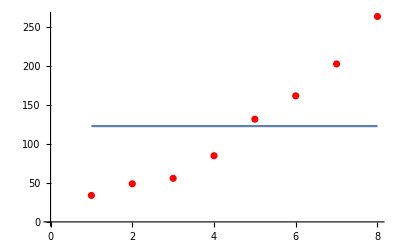

```mathematica
Show[ListPlot[SumHistory1,PlotStyle->Red],Plot[M*(1-Exp[-(P+Q)*t])/(1+Q/P*Exp[-(P+Q)*t])+c/.{P->-234.7883578412975,Q->-6210.624591581776,M->79.51959206572393,c->126.13118312195317},{t,1,8}]]
```

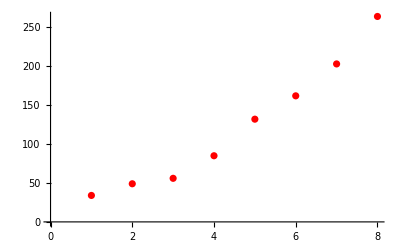

```mathematica
Show[ListPlot[SumHistory1,PlotStyle->Red],Plot[((1-ⅇ^(-(P+Q) t)) M)/(1+(Q ⅇ^(-(P+Q) t))/P)/.{P->58.67082244502255,Q->133.77656828198047,M->735.75},{t,1,8}]]
```